I will be using numerical calculation to plot how the coefficient for the momentum tail of HCB changes with time. Analytic calculation indicates that the momentum tail decays like (1+t^2)^-3/2

```mathematica
Subscript[ϕ, n_][x_] = 1/π^(1/4)/Sqrt[2^n*Factorial[n]] * HermiteH[n,x]*E^(-x^2/2);
b[t_]=Sqrt[1+t^2];
τ[t_]=ArcTan[t];
Subscript[Φ, n_][x_,t_]=b[t]^(-1/2)Subscript[ϕ, n][x/b[t]]*E^(I*(x^2*b'[t]/(2*b[t])-(n+1/2)τ[t]));
t ≥0;
Subscript[ψ, F][x_,y_,t_] = 1/Sqrt[2] * (Subscript[Φ, 0][x,t]Subscript[Φ, 1][y,t] - Subscript[Φ, 0][y,t]Subscript[Φ, 1][x,t] );
Subscript[ψ, B][x_,y_,t_]=Sign[y-x]Subscript[ψ, F][x,y,t];
Subscript[ρ, F][x_,y_]=Integrate[Subscript[ψ, F][x,Subscript[x, 2],0]*Subscript[ψ, F][y,Subscript[x, 2],0],{Subscript[x, 2],-Infinity,Infinity}];
ρ[x_,y_]=Subscript[ρ, F][x,y]-2*Sign[y-x]Integrate[Subscript[ψ, F][x,Subscript[x, 2],0]*Subscript[ψ, F][y,Subscript[x, 2],0],{Subscript[x, 2],x,y}];
Subscript[ρ, B][x_,y_,t_]=1/b[t]*ρ[x/b[t],y/b[t]]*E^(-I*(b'[t](x^2-y^2))/(2*b[t]));
Subscript[n, B][p_,t_] := 2/(2π)*NIntegrate[E^(I*p*(x-y))Subscript[ρ, B][x,y,t],{x,-∞, ∞},{y,-∞, ∞},Method->{"LocalAdaptive", Method->"CartesianRule"}, AccuracyGoal->13,PrecisionGoal->13];
```

```mathematica
Pdomain=Range[19,22,1];
Tdomain = {0,0.25,.5,0.75,1,1.5,2,3,4};
(* Set interopolation functions for various points in time *)
Subscript[dataSet, m_]:=Re[Subscript[n, B][Pdomain,Tdomain[[m]] ]]
Do[Subscript[dataSet, i]=Subscript[dataSet, i],{i,1,Length[Tdomain]}]
```

```mathematica
Subscript[dataSet, 8]
```

{1.24219×10^-7,1.01105×10^-7,8.31221×10^-8,6.89647×10^-8}

```mathematica
Subscript[dataSet, 1]={3.9580362200893295*^-6,3.218980275591806*^-6,2.644829451525684*^-6,2.1932915511092933*^-6};
Subscript[dataSet, 2]={3.6121798765860894*^-6,2.9378493777099995*^-6,2.4139452060278866*^-6,2.001898059535035*^-6};
Subscript[dataSet, 3]={2.8273395711441986*^-6,2.2997982961075907*^-6,1.8898692040676803*^-6,1.5674173887964096*^-6};
Subscript[dataSet, 4]={2.020345520416006*^-6,1.6435976793733223*^-6,1.3507889534056279*^-6,1.120426727891506*^-6};
Subscript[dataSet, 5]={1.3934720529875518*^-6,1.1337537321632996*^-6,9.318682069578357*^-7,7.730139305802488*^-7};
Subscript[dataSet, 6]={6.716099791487755*^-7,5.46520261065932*^-7,4.4926337627327115*^-7,3.7272216881402454*^-7};
Subscript[dataSet, 7]={3.5163624128663697*^-7,2.8617072251346094*^-7,2.352596999474896*^-7,1.9519391916885244*^-7};
Subscript[dataSet, 8]={1.2421858118405126*^-7,1.0110509209412211*^-7,8.312214786345061*^-8,6.896467210913741*^-8};
Subscript[dataSet, 9]={5.6030077841479046*^-8,4.5595844416419506*^-8,3.7478174161899054*^-8,3.112805956730622*^-8};
```

```mathematica
Subscript[dataSet, 1]={1.008206978082305,1.0076054768543117,1.0070679189248497,1.0065854970908332};
Subscript[dataSet, 2]={0.9267521200552173,0.9253996355643164,0.9242392381256247,0.923235504106521};
Subscript[dataSet, 3]={0.7253910467355561,0.7244185223506315,0.7235836459596984,0.722861674298683};
Subscript[dataSet, 4]={0.5183461395225929,0.5177204471564871,0.517183302274884,0.5167184862447943};
Subscript[dataSet, 5]={0.3575135301856643,0.3571235811215802,0.3567890271417587,0.35649862513297936};
Subscript[dataSet, 6]={0.17231034812547047,0.17214961878445625,0.17201170911737637,0.17189203904649147};
Subscript[dataSet, 7]={0.09021688931189971,0.09014154514945148,0.09007505443709685,0.0900195469514761};
Subscript[dataSet, 8]={0.031869906094314344,0.03184731528017533,0.0318253912395531,0.031805132892235626};
Subscript[dataSet, 9]={0.014375251288849266,0.01436233529408905,0.014349455425597965,0.014355640952644034};
```

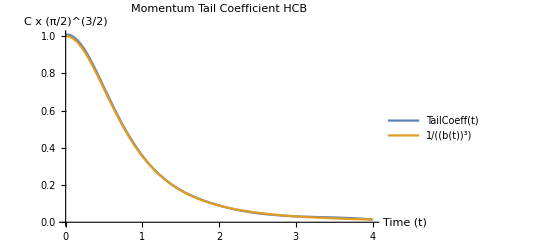

C:/Users/Tim/Documents/PhysicsResearch/UltraColdAtoms/MomentumTailCoeffTimeDep.png

```mathematica
(* Prepare domains and ranges for extracting the coefficient*)
CoeffDep={};
Do[CoeffDep=Append[CoeffDep,Mean[Subscript[dataSet, i]]],{i,1,Length[Tdomain]}]
TailCoeff=Interpolation[Thread[{Tdomain,CoeffDep}]];
p1=Plot[{TailCoeff[t],b[t]^(-3)},{t,0,4},PlotLabel->"Momentum Tail Coefficient HCB",AxesLabel->{"Time (t)", "C x (π/2)^(3/2)"},PlotLegends->"Expressions",ImageSize->Scaled[.5]]
Export["C:/Users/Tim/Documents/PhysicsResearch/UltraColdAtoms/MomentumTailCoeffTimeDep.png",p1]
```

```mathematica
A=Re[Subscript[n, B][Range[26,29,1],Tdomain[[1]] ]]
```

{1.12067×10^-6,9.63065×10^-7,8.32237×10^-7,7.22901×10^-7}

```mathematica
Range[26,29,1]^4 *(π/2)^(3/2)*A
```

{1.00821,1.00761,1.00707,1.00659}

```mathematica
TailCoeff[0]
```

1.00737